```mathematica
Quit
```

# Functions

## Stabilizer State → GraphState

## GottesmanGraphsystem

```mathematica
<<Q3`
<<LocalCliffordEquivalent`
```

```mathematica
?GottesmanGraphsystem
```

```mathematica
Let[Qubit,S]
```

```mathematica
ss=S[Range@4,];
ket=S[1,7]**(Ket[]+Ket[ss->1])/Sqrt[2]
```

(␣+ⅈ 1_S_11_S_21_S_31_S_4)/(√2)

```mathematica
gnr=StabilizerStandardGenerator[ket]
```

{S_1^x S_2^x S_3^x S_4^y,S_1^z S_4^z,S_2^z S_4^z,S_3^z S_4^z}

```mathematica
gotvecs=GottesmanVector[#,ss]&/@gnr;
gotvecs//MatrixForm
```

(1 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1)


{(1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),-Graphics-}

```mathematica
{lop,gr}=GottesmanGraphsystem[gotvecs];
{lop//MatrixForm,gr}
```

```mathematica
newgnr=StabilizerStandardGenerator[gr,ss]
newgotvecs=GottesmanVector[#,ss]& /@ newgnr;
newgotvecs//MatrixForm
```

{S_1^x S_2^z S_3^z S_4^z,S_1^z S_2^x,S_1^z S_3^x,S_1^z S_4^x}

(1 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
GottesmanReduce[gotvecs.lop]==newgotvecs
```

True

## QuissoGraphsystem

```mathematica
<<Q3`
<<LocalCliffordEquivalent`
```

```mathematica
?QuissoGraphsystem
```

```mathematica
Let[Qubit,S]
```

```mathematica
ss=S[Range@4,];
ket=S[1,7]**(Ket[]+Ket[ss->1])/Sqrt[2]
```

(␣+ⅈ 1_S_11_S_21_S_31_S_4)/(√2)

```mathematica
{lop,gr}=QuissoGraphsystem[ket]
```

{{S_1^z S_1^S,S_2^H,S_3^H,S_4^H},-Graphics-}

```mathematica
MultiplyFold[ ReleaseHold @ lop][ket]==GraphState[gr]
```

True

```mathematica
newss=S[Range@5,]
```

{S_1,S_2,S_3,S_4,S_5}

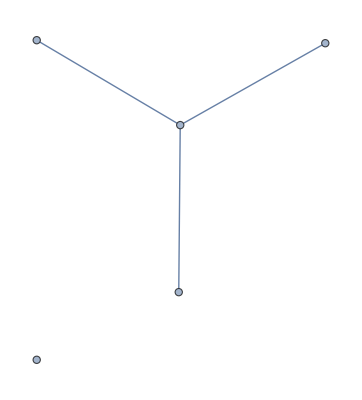
{{S_1^z S_1^S,S_2^H,S_3^H,S_4^H,S_5^H},-Graphics-}

```mathematica
{lop,gr}=QuissoGraphsystem[ket,newss]
```

```mathematica
MultiplyFold[ ReleaseHold @ lop][ket]==GraphState[gr]
```

True

```mathematica
gnr=StabilizerStandardGenerator[ket]
```

{S_1^x S_2^x S_3^x S_4^y,S_1^z S_4^z,S_2^z S_4^z,S_3^z S_4^z}

```mathematica
{lop,gr}=QuissoGraphsystem[gnr]
```

{{S_1^z S_1^S,S_2^H,S_3^H,S_4^H},-Graphics-}

```mathematica
MultiplyFold[ ReleaseHold @ lop][ket]==GraphState[gr]
```

True

## Compare Two Graph States

## GottesmanLocalEquivalent

```mathematica
<<Q3`
<<LocalCliffordEquivalent`
```

```mathematica
?GottesmanLocalEquivalent
```

```mathematica
Let[Qubit,S];
```

```mathematica
n=4;
ss=S[ Range @ n ,];
```

```mathematica
edges1=UndirectedEdge@@#&/@{S[{1,2},],S[{1,3},],S[{1,4},]};
edges2=UndirectedEdge@@#&/@{S[{1,2},],S[{1,3},],S[{1,4},],S[{2,3},],S[{2,4},],S[{3,4},]};
```

```mathematica
(*Options for graph*)
circleLayout[n_]:=Table[{Cos[2 Pi/n u],Sin[2 Pi/n u]},{u,1,n}];
options[ss_]:={GraphLayout->"CircularEmbedding",ImageSize->Small,VertexCoordinates->Thread[ss->circleLayout[Length @ ss]],VertexLabels->"Name"};
```

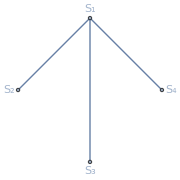
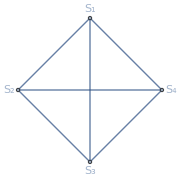

```mathematica
gr1=Graph[edges1,Sequence @@ options[ss] ];
gr2=Graph[edges2,Sequence @@ options[ss]];
{gr1,gr2}
```

```mathematica
lops=GottesmanLocalEquivalent[gr1,gr2];
MatrixForm/@lops
```

{(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)}

As this is subcode of LocalEquivalent, let’s check if this local clifford operators transform gr1 to gr2.

## LocalEquivalent

```mathematica
<<Q3`
<<LocalCliffordEquivalent`
```

```mathematica
?LocalEquivalent
```

```mathematica
Let[Qubit,S];
```

```mathematica
n=4;
ss=S[ Range @ n ,];
```

```mathematica
edges1=UndirectedEdge@@#&/@{S[{1,2},],S[{1,3},],S[{1,4},]};
edges2=UndirectedEdge@@#&/@{S[{1,2},],S[{1,3},],S[{1,4},],S[{2,3},],S[{2,4},],S[{3,4},]};
```

```mathematica
(*Options for graph*)
circleLayout[n_]:=Table[{Cos[2 Pi/n u],Sin[2 Pi/n u]},{u,1,n}];
options[ss_]:={GraphLayout->"CircularEmbedding",ImageSize->Small,VertexCoordinates->Thread[ss->circleLayout[Length @ ss]],VertexLabels->"Name"};
```

```mathematica
gr1=Graph[edges1,Sequence @@ options[ss] ];
gr2=Graph[edges2,Sequence @@ options[ss]];
{gr1,gr2}
```

{-Graphics-,-Graphics-}

```mathematica
lops=LocalEquivalent[gr1,gr2]
```

{{S_1^S S_1^H,S_2^z S_2^H S_2^S,S_3^z S_3^H S_3^S,S_4^z S_4^H S_4^S},{S_1^z S_1^H S_1^S S_1^H,S_2^S,S_3^z S_3^H S_3^S,S_4^z S_4^H S_4^S},{S_1^z S_1^H S_1^S S_1^H,S_2^z S_2^H S_2^S,S_3^S,S_4^z S_4^H S_4^S},{S_1^z S_1^S S_1^H,S_2^z S_2^S,S_3^z S_3^S,S_4^H S_4^S},{S_1^z S_1^H S_1^S S_1^H,S_2^z S_2^H S_2^S,S_3^z S_3^H S_3^S,S_4^S},{S_1^z S_1^S S_1^H,S_2^z S_2^S,S_3^H S_3^S,S_4^z S_4^S},{S_1^z S_1^S S_1^H,S_2^H S_2^S,S_3^z S_3^S,S_4^z S_4^S},{S_1^H S_1^S S_1^H,S_2^z S_2^S,S_3^z S_3^S,S_4^z S_4^S}}

```mathematica
Abs[Dagger@GraphState[gr2]**MultiplyFold[ ReleaseHold @ #][GraphState[gr1]]]&/@lops
```

{1,1,1,1,1,1,1,1}

```mathematica
LocalEquivalentQ[gr1,gr2]
```

True

```mathematica
paths=FindLocalComplementPath[gr1,ReleaseHold@#]&/@lops
```

{{S_2,S_1,S_3,S_4,S_3},{S_1,S_3,S_4,S_3},{S_1,S_2,S_4,S_2},{S_4,S_1},{S_1,S_2,S_3,S_2},{S_3,S_1},{S_2,S_1},{S_1}}

```mathematica
(*Visualization of the orbit*)
showprocess[vtx_List,gr_Graph,opts___?OptionQ]:=FoldList[GraphLocalComplement[#1,#2,opts]&,gr,vtx];
```

Look for one of lops.

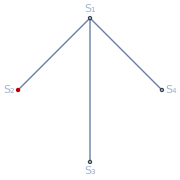
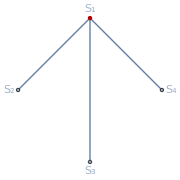
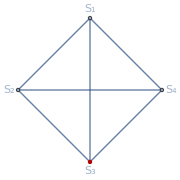
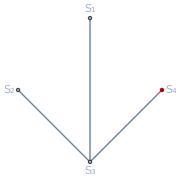
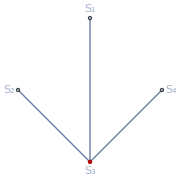
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
vtx=paths[[1]];
grs=showprocess[vtx,gr1,Sequence @@ options[ss]];
highlightgrs=MapThread[ Graph[#1,GraphHighlight->#2]&,{Most @ grs, vtx}];
AppendTo[highlightgrs,Last@grs]
```

## LocalEquivalentQ

```mathematica
<<Q3`
<<LocalCliffordEquivalent`
```

```mathematica
?LocalEquivalentQ
```

See LocalEquivalent for example.

## Function for Graph

## GraphLocalComplement

```mathematica
<<Q3`
<<LocalCliffordEquivalent`
```

```mathematica
?GraphLocalComplement
```

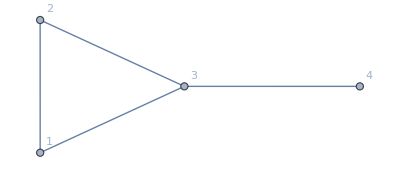

```mathematica
gr=Graph[{1<->2,1<->3,2<->3,3<->4},VertexLabels->Automatic]
```

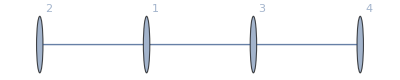

```mathematica
GraphLocalComplement[gr,1,VertexLabels->Automatic]
```

## FindLocalComplementPath

See LocalEquivalent for example.

## Useful Sub-functions

## GraphStateQ

```mathematica
<<Q3`
<<LocalCliffordEquivalent`
```

```mathematica
?GraphStateQ
```

```mathematica
Let[Qubit,S]
```

Consider a graph connecting qubits.

```mathematica
g=Graph[{S[1]<->S[2],S[1]<->S[3],S[1]<->S[4]}]
```

-Graphics-

Get the graph state associated with the graph.

```mathematica
ket=GraphState[g]
```

␣/4+(1_S_1)/4-1/4 1_S_11_S_2+1/4 1_S_11_S_21_S_3-1/4 1_S_11_S_21_S_31_S_4+1/4 1_S_11_S_21_S_4-1/4 1_S_11_S_3+1/4 1_S_11_S_31_S_4-1/4 1_S_11_S_4+(1_S_2)/4+1/4 1_S_21_S_3+1/4 1_S_21_S_31_S_4+1/4 1_S_21_S_4+(1_S_3)/4+1/4 1_S_31_S_4+(1_S_4)/4

Test whether the state is graph state:

```mathematica
GraphStateQ[ket]
```

True

Operate a operator to the graph state to be not a graph state:

```mathematica
newket=S[1,7]**ket
```

␣/4+(ⅈ 1_S_1)/4-1/4 ⅈ 1_S_11_S_2+1/4 ⅈ 1_S_11_S_21_S_3-1/4 ⅈ 1_S_11_S_21_S_31_S_4+1/4 ⅈ 1_S_11_S_21_S_4-1/4 ⅈ 1_S_11_S_3+1/4 ⅈ 1_S_11_S_31_S_4-1/4 ⅈ 1_S_11_S_4+(1_S_2)/4+1/4 1_S_21_S_3+1/4 1_S_21_S_31_S_4+1/4 1_S_21_S_4+(1_S_3)/4+1/4 1_S_31_S_4+(1_S_4)/4

Test whether the state is graph state:

```mathematica
GraphStateQ[newket]
StabilizerStateQ[newket]
```

False

True

## StabilizerStandardGenerator

```mathematica
<<Q3`
<<LocalCliffordEquivalent`
```

```mathematica
?StabilizerStandardGenerator
```

```mathematica
Let[Qubit,S]
```

```mathematica
grp=CliffordGroup[S@{1,2,3}];
op=First@GroupElements[grp,{201}];
ket=op**Ket[]
```

-1/2 1_S_11_S_2+1/2 1_S_11_S_21_S_3+(ⅈ 1_S_2)/2+1/2 ⅈ 1_S_21_S_3

```mathematica
gnr=StabilizerStandardGenerator[ket,S@{1,2,3}]
```

{S_1^y S_3^z,S_1^z S_3^x,-S_2^z}

```mathematica
stb=Multiply@@@Subsets[gnr]
```

{1,S_1^y S_3^z,S_1^z S_3^x,-S_2^z,-S_1^x S_3^y,-S_1^y S_2^z S_3^z,-S_1^z S_2^z S_3^x,S_1^x S_2^z S_3^y}

```mathematica
stb**ket-ket
```

{0,0,0,0,0,0,0}

```mathematica
stb0=Stabilizer[ket,S@{1,2,3}]
```

{1,-S_2^z,-S_1^x S_3^y,S_1^x S_2^z S_3^y,S_1^y S_3^z,-S_1^y S_2^z S_3^z,S_1^z S_3^x,-S_1^z S_2^z S_3^x}

```mathematica
ContainsAll[stb,stb0]
ContainsAll[stb0,stb]
```

True

True

```mathematica
$n=3;
grp=CliffordGroup[$n];
op=First@GroupElements[grp,{203}];
ket=op**(Ket@@Table[0,$n])
```

(0,0,0)/2+(0,0,1)/2-(1,1,0)/2+(1,1,1)/2

```mathematica
gnr=StabilizerStandardGenerator[ket]
stb=Prepend[ Multiply@@@Rest@Subsets[gnr] , Pauli[0,0,0]]
```

{-(σ^x⊗σ^x⊗σ^z),σ^0⊗σ^z⊗σ^x,σ^z⊗σ^z⊗σ^0}

{σ^0⊗σ^0⊗σ^0,-(σ^x⊗σ^x⊗σ^z),σ^0⊗σ^z⊗σ^x,σ^z⊗σ^z⊗σ^0,-(σ^x⊗σ^y⊗σ^y),σ^y⊗σ^y⊗σ^z,σ^z⊗σ^0⊗σ^x,-(σ^y⊗σ^x⊗σ^y)}

```mathematica
stb**ket-ket
```

{0,0,0,0,0,0,0,0}

```mathematica
stb0=Stabilizer[ket]
```

{σ^0⊗σ^0⊗σ^0,σ^0⊗σ^z⊗σ^x,-(σ^x⊗σ^x⊗σ^z),-(σ^x⊗σ^y⊗σ^y),-(σ^y⊗σ^x⊗σ^y),σ^y⊗σ^y⊗σ^z,σ^z⊗σ^0⊗σ^x,σ^z⊗σ^z⊗σ^0}

```mathematica
ContainsAll[stb,stb0]
ContainsAll[stb0,stb]
```

True

True

```mathematica
vec=Matrix[ket];
vec//Normal
```

{1/2,1/2,0,0,0,0,-1/2,1/2}

```mathematica
gnr=StabilizerStandardGenerator[vec];
stb=Prepend[ Dot@@@Rest@Subsets[gnr] , ThePauli[0,0,0]];
MatrixForm/@stb
```

{(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0),(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
(#.vec-vec)&/@stb//Normal//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
stb0=Stabilizer[vec];
```

```mathematica
ContainsAll[stb,stb0]
ContainsAll[stb0,stb]
```

True

True

```mathematica
gr=Graph[{S[1]<->S[2],S[1]<->S[3],S[1]<->S[4]}]
```

-Graphics-

```mathematica
gnr=StabilizerStandardGenerator[gr]
```

{S_1^x S_2^z S_3^z S_4^z,S_1^z S_2^x,S_1^z S_3^x,S_1^z S_4^x}

```mathematica
stb=Multiply@@@Subsets[gnr]
```

{1,S_1^x S_2^z S_3^z S_4^z,S_1^z S_2^x,S_1^z S_3^x,S_1^z S_4^x,S_1^y S_2^y S_3^z S_4^z,S_1^y S_2^z S_3^y S_4^z,S_1^y S_2^z S_3^z S_4^y,S_2^x S_3^x,S_2^x S_4^x,S_3^x S_4^x,-S_1^x S_2^y S_3^y S_4^z,-S_1^x S_2^y S_3^z S_4^y,-S_1^x S_2^z S_3^y S_4^y,S_1^z S_2^x S_3^x S_4^x,-S_1^y S_2^y S_3^y S_4^y}

```mathematica
ket=GraphState[gr];
stb**ket-ket
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
stb0=Stabilizer[ket]
```

{1,S_3^x S_4^x,S_2^x S_4^x,S_2^x S_3^x,-S_1^x S_2^y S_3^y S_4^z,-S_1^x S_2^y S_3^z S_4^y,-S_1^x S_2^z S_3^y S_4^y,S_1^x S_2^z S_3^z S_4^z,-S_1^y S_2^y S_3^y S_4^y,S_1^y S_2^y S_3^z S_4^z,S_1^y S_2^z S_3^y S_4^z,S_1^y S_2^z S_3^z S_4^y,S_1^z S_4^x,S_1^z S_3^x,S_1^z S_2^x,S_1^z S_2^x S_3^x S_4^x}

```mathematica
ContainsAll[stb,stb0]
ContainsAll[stb0,stb]
```

True

True

## GottesmanReduce

```mathematica
<<Q3`
<<LocalCliffordEquivalent`
```

```mathematica
?GottesmanReduce
```

```mathematica
Let[Qubit,S]
```

```mathematica
ss=S[Range@3,]
ops={S[1,1]**S[2,2]**S[3,3],S[2,1]**S[3,2]}
gmats=GottesmanVector[#,ss]&/@ops
```

{S_1,S_2,S_3}

{S_1^x S_2^y S_3^z,S_2^x S_3^y}

{{1,0,1,1,0,1},{0,0,1,0,1,1}}

```mathematica
GottesmanReduce[gmats]//MatrixForm
```

(1 | 0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1 | 1)

```mathematica
GottesmanSplit[gmats];
GottesmanReduce[%];
GottesmanMerge@@%//MatrixForm
```

(1 | 0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1 | 1)

## GottesmanReducesystem

```mathematica
<<Q3`
<<LocalCliffordEquivalent`
```

```mathematica
?GottesmanReducesystem
```

```mathematica
Let[Qubit,S]
```

```mathematica
ss=S[Range@3,]
ops={S[1,1]**S[2,2]**S[3,3],S[2,1]**S[3,2]}
gmats=GottesmanVector[#,ss]&/@ops;
gmats//MatrixForm
```

{S_1,S_2,S_3}

{S_1^x S_2^y S_3^z,S_2^x S_3^y}

(1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 1)

```mathematica
{newgmats,op}=GottesmanReducesystem[gmats];
MatrixForm/@{newgmats,op}
```

{(1 | 0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1 | 1),(1 | 1
0 | 1)}

```mathematica
Mod[op.newgmats,2]==gmats
```

True

```mathematica
{xx,zz}=GottesmanSplit[gmats]
```

{{{1,1,0},{0,1,1}},{{0,1,1},{0,0,1}}}

```mathematica
{newxx,newzz,op}=GottesmanReducesystem[{xx,zz}];
MatrixForm/@{newxx,newzz,op}
```

{(1 | 0 | 1
0 | 1 | 1),(0 | 1 | 0
0 | 0 | 1),(1 | 1
0 | 1)}

```mathematica
Mod[op.newxx,2]==xx
Mod[op.newzz,2]==zz
```

True

True

## MultiplyFold

```mathematica
<<Q3`
<<LocalCliffordEquivalent`
```

```mathematica
?MultiplyFold
```

```mathematica
Let[Qubit,S]
```

```mathematica
oplist={S[1,1],S[2,1],S[3,1]}
```

{S_1^x,S_2^x,S_3^x}

```mathematica
MultiplyFold[Ket[],oplist]
```

1_S_11_S_21_S_3

```mathematica
MultiplyFold[oplist]@Ket[]
```

1_S_11_S_21_S_3

## SupermapFold

```mathematica
?SupermapFold
```

```mathematica
<<Q3`
<<LocalCliffordEquivalent`
```

```mathematica
?MultiplyFold
```

```mathematica
Let[Qubit,S]
```

```mathematica
oplist={S[1,1],S[2,1],S[3,1]}
```

{S_1^x,S_2^x,S_3^x}

```mathematica
SupermapFold[Dyad[Ket[]],oplist]
```

1_S_11_S_21_S_31_S_11_S_21_S_3

```mathematica
SupermapFold[oplist]@Dyad[Ket[]]
```

1_S_11_S_21_S_31_S_11_S_21_S_3

# Example : Finding Local Clifford Operators of Two stabilizer States

```mathematica
<<Q3`
<<LocalCliffordEquivalent`
```

```mathematica
(*Options for graph*)
circleLayout[n_]:=Table[{Cos[2 Pi/n u],Sin[2 Pi/n u]},{u,1,n}];
options[ss_]:={GraphLayout->"CircularEmbedding",ImageSize->Small,VertexCoordinates->Thread[ss->circleLayout[Length @ ss]],VertexLabels->"Name"};

(*construct random local Clifford operator*)
RandomLocalCliffordOperator[ ss_ ]:= Module[
{ls = Length @ ss , gr , cl , clList , q},
Let[Qubit,q];
cl={{{1,0},{0,1}},{{1,1},{0,1}},{{1,0},{1,1}},{{0,1},{1,0}},{{1,1},{1,0}},{{0,1},{1,1}}};
cl=FromGottesmanMatrix[#,q]&/@cl;
cl=Flatten @ Outer[ Multiply , q[{0,1,2,3}],cl ];
clList=(RandomChoice[cl]/.q->#)&/@ss
]
```

```mathematica
ss=S[Range@5,]
```

{S_1,S_2,S_3,S_4,S_5}

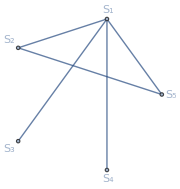

```mathematica
edges=UndirectedEdge@@#&/@{S[{1,2},],S[{1,3},],S[{1,4},],S[{1,5},],S[{2,5},]};
graph= Graph[edges,options[ss]]
```

```mathematica
ket0=GraphState[graph];
ket1=MultiplyFold[RandomLocalCliffordOperator[ss]][ket0];
ket2=MultiplyFold[RandomLocalCliffordOperator[ss]][ket0];
```

```mathematica
ket1===ket2
```

False

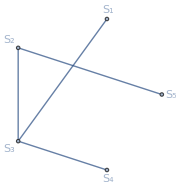
{{S_1^z,S_2^0,S_3^S,S_4^z S_4^S,S_5^z},-Graphics-}

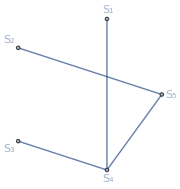
{{S_1^0,S_2^z,S_3^z,S_4^0,S_5^0},-Graphics-}

```mathematica
{lop1,gr1}=QuissoGraphsystem[ket1,ss,options[ss]]
{lop2,gr2}=QuissoGraphsystem[ket2,ss,options[ss]]
```

```mathematica
lops=LocalEquivalent[gr1,gr2];
Length@lops
```

8

```mathematica
lop0=Dagger@lop2**#**lop1&/@lops
```

{{S_1^z,(S_2^z)^†S_2^H,(S_3^z)^†S_3^H S_3^S,S_4^H S_4^z S_4^S,S_5^H S_5^z},{S_1^H S_1^S S_1^H S_1^z,(S_2^z)^†S_2^H,(S_3^z)^†S_3^H S_3^S S_3^S,S_4^z S_4^H S_4^z S_4^S,S_5^H S_5^z},{S_1^H S_1^S S_1^H S_1^z,(S_2^z)^†S_2^H,(S_3^z)^†S_3^H S_3^S,S_4^z S_4^S S_4^H S_4^z S_4^S,S_5^H S_5^z},{S_1^z,(S_2^z)^†S_2^H,(S_3^z)^†S_3^H S_3^S S_3^S,S_4^z S_4^S S_4^H S_4^z S_4^S,S_5^H S_5^z},{S_1^z,(S_2^z)^†S_2^H S_2^S,(S_3^z)^†S_3^H S_3^S,S_4^H S_4^z S_4^S,S_5^z S_5^S S_5^H S_5^z},{S_1^H S_1^S S_1^H S_1^z,(S_2^z)^†S_2^H S_2^S,(S_3^z)^†S_3^H S_3^S S_3^S,S_4^z S_4^H S_4^z S_4^S,S_5^z S_5^S S_5^H S_5^z},{S_1^H S_1^S S_1^H S_1^z,(S_2^z)^†S_2^H S_2^S,(S_3^z)^†S_3^H S_3^S,S_4^z S_4^S S_4^H S_4^z S_4^S,S_5^z S_5^S S_5^H S_5^z},{S_1^z,(S_2^z)^†S_2^H S_2^S,(S_3^z)^†S_3^H S_3^S S_3^S,S_4^z S_4^S S_4^H S_4^z S_4^S,S_5^z S_5^S S_5^H S_5^z}}

```mathematica
Abs[Dagger@ket2**MultiplyFold[ ReleaseHold @ #][ket1]]&/@lop0
```

{1,1,1,1,1,1,1,1}